## Intel

```mathematica
INTC = Import[NotebookDirectory[]<>"bytick/scores/basic/INTC.csv"];
```

## Snapshotting

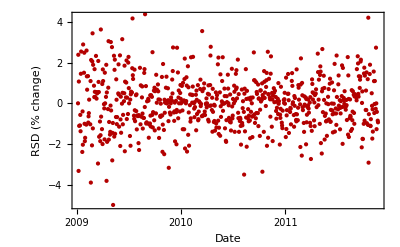

```mathematica
RSD1=DateListPlot[INTC[[All,{1,3}]],PlotStyle->{RGBColor[.7,0,0]},
FrameLabel->{"Date","RSD (% change)"},FrameTicks->{Automatic,All}]
```

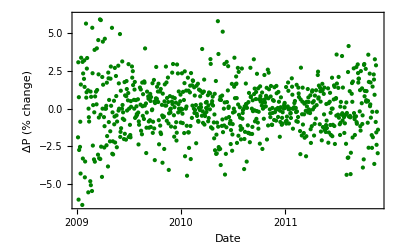

```mathematica
DPC1=DateListPlot[INTC[[All,{1,4}]],PlotStyle->{RGBColor[0,.5,0]},
FrameLabel->{"Date","ΔP (% change)"},FrameTicks->{Automatic,All}]
```

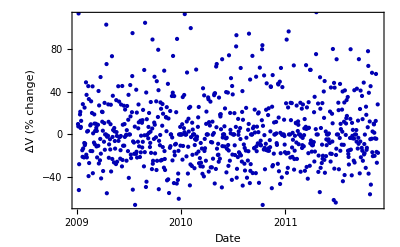

```mathematica
DVC1=DateListPlot[INTC[[All,{1,5}]],PlotStyle->{RGBColor[0,0,.7]},FrameTicks->{Automatic,All},
FrameLabel->{"Date","ΔV (% change)"},FrameTicks->{Automatic,All}]
```

```mathematica
Export[NotebookDirectory[]<>"Figures/INTC_RSD1.pdf",RSD1];
Export[NotebookDirectory[]<>"Figures/INTC_DPC1.pdf",DPC1];
Export[NotebookDirectory[]<>"Figures/INTC_DVC1.pdf",DVC1];
```

## Histogramming over 60 days

Static figure for the paper:

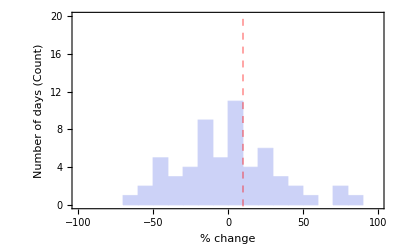

```mathematica
DVC60Histo20091013=Histogram[INTC[[197;;197+60,5]],{-100,100,10},PlotRange->{0,20},
FrameLabel->{"% change","Number of days (Count)"},Frame->True,FrameTicks->{Automatic,All},
GridLines->{{10},None},GridLinesStyle->Directive[Red,Dashed,Thick]]
```

```mathematica
Export[NotebookDirectory[]<>"Figures/INTC_DVC60_Histo_20091013.pdf",DVC60Histo20091013];
```

Interactive Histograms :

```mathematica
Manipulate[Histogram[INTC[[date;;date+60,3]],{-10,10,1},PlotRange->{0,35},PlotLabel->"  RSD — 60 Days"INTC[[date,1]]],{date,1,650,1}]
```

```mathematica
Manipulate[Histogram[INTC[[date;;date+60,4]],{-10,10,1},PlotRange->{0,35},PlotLabel->"  ΔPrice — 60 Days"INTC[[date,1]]],{date,1,650,1}]
```

```mathematica
Manipulate[Histogram[INTC[[date;;date+60,5]],{-100,100,10},PlotRange->{0,20},PlotLabel->"  ΔVol — 60 Days"INTC[[date,1]]],{date,1,650,1}]
```

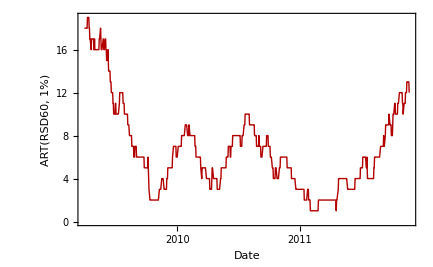

```mathematica
RSD60=DateListPlot[INTC[[All,{1,7}]][[60;;]],FrameLabel->{"Date","ART(RSD60, 1%)"},PlotStyle->{RGBColor[.7,0,0]},Joined->True,Frame->True,FrameTicks->{Automatic,All}]
```

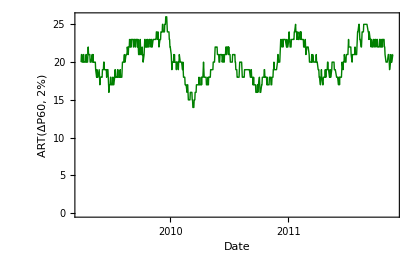

```mathematica
DPC60=DateListPlot[INTC[[All,{1,8}]][[60;;]],
FrameLabel->{"Date","ART(ΔP60, 2%)"},PlotStyle->{RGBColor[0,.5,0]},Joined->True,Frame->True,FrameTicks->{Automatic,All}]
```

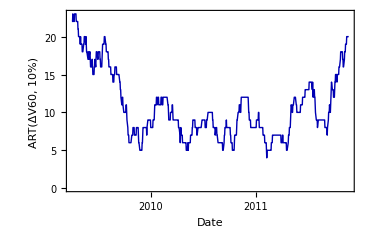

```mathematica
DVC60=DateListPlot[INTC[[All,{1,9}]][[60;;]],
FrameLabel->{"Date","ART(ΔV60, 10%)"},PlotStyle->{RGBColor[0,0,.7]}, Joined->True,Frame->True,FrameTicks->{Automatic,All}]
```

```mathematica
Export[NotebookDirectory[]<>"Figures/INTC_RSD60.pdf",RSD60];
Export[NotebookDirectory[]<>"Figures/INTC_DPC60.pdf",DPC60];
Export[NotebookDirectory[]<>"Figures/INTC_DVC60.pdf",DVC60];
```

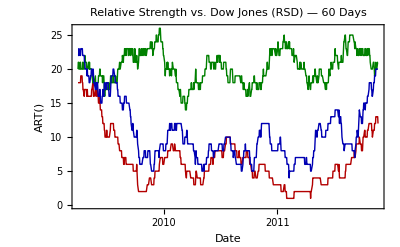

```mathematica
DateListPlot[{INTC[[All,{1,7}]][[60;;]],INTC[[All,{1,8}]][[60;;]],INTC[[All,{1,9}]][[60;;]]},PlotLabel->"Relative Strength vs. Dow Jones (RSD) — 60 Days",FrameLabel->{"Date","ART()"},PlotStyle->{RGBColor[.7,0,0],RGBColor[0,.5,0],RGBColor[0,0,.7]},Joined->True,Frame->True,FrameTicks->{Automatic,All}]
```

## Scoring

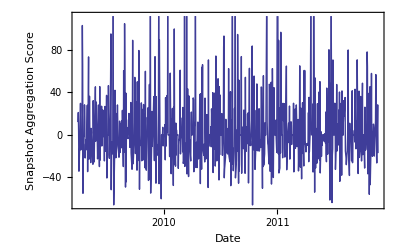

```mathematica
SScore=DateListPlot[INTC[[All,{1,5}]][[60;;]],
FrameLabel->{"Date","Snapshot Aggregation Score"},Joined->True, FrameTicks->{Automatic,All}]
```

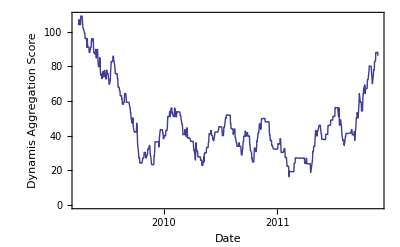

```mathematica
HScore=DateListPlot[INTC[[All,{1,10}]][[60;;]],
FrameLabel->{"Date","Dynamis Aggregation Score"},Joined->True,FrameTicks->{Automatic,All}]
```

```mathematica
Export[NotebookDirectory[]<>"Figures/INTC_SScore.pdf",SScore];
Export[NotebookDirectory[]<>"Figures/INTC_HScore.pdf",HScore];
```

Validate that Python and Mathematica compute the same score

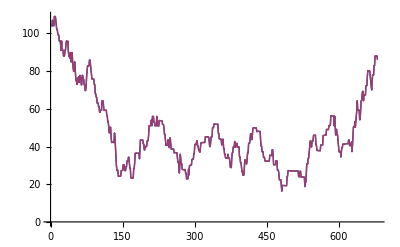

```mathematica
ListPlot[{0.1*INTC[[All,8]][[60;;]]+2*INTC[[All,7]][[60;;]]+3*INTC[[All,9]][[60;;]],
INTC[[All,10]][[60;;]]},Joined->True]
```

Building a scoring function

```mathematica
Manipulate[ListPlot[{a*INTC[[All,8]][[60;;]]+b*INTC[[All,7]][[60;;]]+c*INTC[[All,9]][[60;;]],
INTC[[All,10]][[60;;]]},Joined->True],{a,0,5},{b,0,5},{c,0,5}]
```

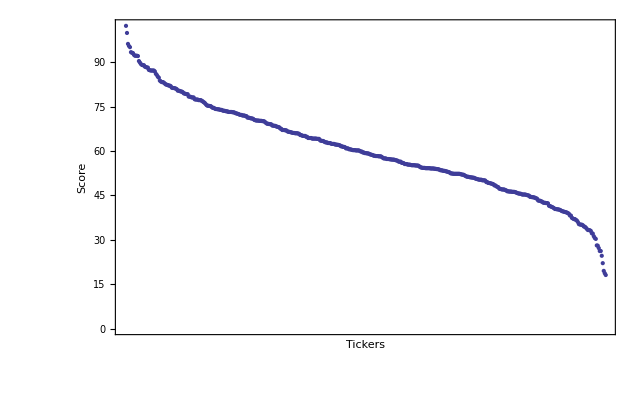

```mathematica
HScore20111003=ListPlot[Sort[Map[#1[[-1]]&,Import[NotebookDirectory[]<>"bydate/scores/basic/2011-10-03.csv"]],Greater],Frame->True,FrameTicks->{None,All},
FrameLabel->{"Tickers","Score"}]
```

```mathematica
Export[NotebookDirectory[]<>"Figures/HScore_20111003.pdf",HScore20111003];
```

## Ranking

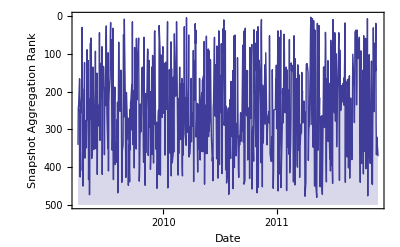

```mathematica
SRank=DateListPlot[{Map[{Partition[#1,3][[1]],500-#1[[-1]]}&,Import[NotebookDirectory[]<>"bytick/ranks/snapshot/INTC.csv"]]}, Joined->True,Filling->Bottom,PlotRange->{Automatic,{0,500}},
FrameLabel->{"Date","Snapshot Aggregation Rank"},
FrameTicks->{Automatic,Table[{x,500-x},{x,0,500,100}]}]
```

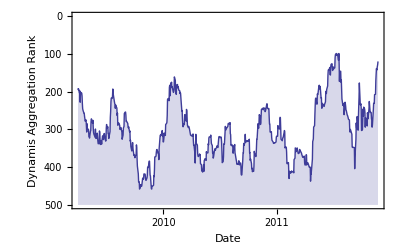

```mathematica
HRank=DateListPlot[{Map[{Partition[#1,3][[1]],500-#1[[-1]]}&,Import[NotebookDirectory[]<>"bytick/ranks/histogram/INTC.csv"]]}, Joined->True,Filling->Bottom,PlotRange->{Automatic,{0,500}},
FrameLabel->{"Date","Dynamis Aggregation Rank"},
FrameTicks->{Automatic,Table[{x,500-x},{x,0,500,100}]}]
```

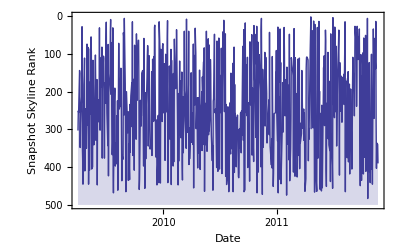

```mathematica
SkylineSnapRank=DateListPlot[{Map[{Partition[#1,3][[1]],500-#1[[-1]]}&,Import[NotebookDirectory[]<>"bytick/ranks/skyline/snapshot/INTC.csv"]]}, Joined->True,Filling->Bottom,PlotRange->{Automatic,{0,500}},
FrameLabel->{"Date","Snapshot Skyline Rank"},
FrameTicks->{Automatic,Table[{x,500-x},{x,0,500,100}]}]
```

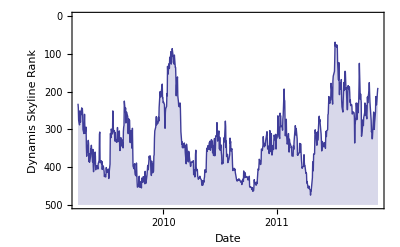

```mathematica
SkylineHistoRank=DateListPlot[{Map[{Partition[#1,3][[1]],500-#1[[-1]]}&,Import[NotebookDirectory[]<>"bytick/ranks/skyline/histogram/INTC.csv"]]}, Joined->True,Filling->Bottom,PlotRange->{Automatic,{0,500}},
FrameLabel->{"Date","Dynamis Skyline Rank"},
FrameTicks->{Automatic,Table[{x,500-x},{x,0,500,100}]}]
```

```mathematica
Export[NotebookDirectory[]<>"Figures/INTC_SRank.pdf",SRank];
Export[NotebookDirectory[]<>"Figures/INTC_HRank.pdf",HRank];
Export[NotebookDirectory[]<>"Figures/INTC_SkylineSnapRank.pdf",SkylineSnapRank];
Export[NotebookDirectory[]<>"Figures/INTC_SkylineHistoRank.pdf",SkylineHistoRank];
```

```mathematica
NotebookSave[EvaluationNotebook[]]
```